# Circle Passing Through 3 Points

```mathematica
pointList = RandomReal[{1, 50},{3,2}];
```

{{23.6908,32.4855},{27.612,39.8108}}

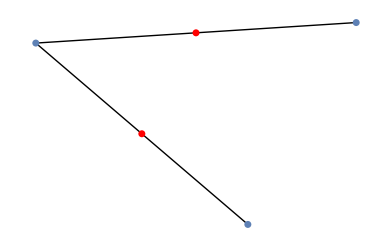

```mathematica
midPoint = {(pointList[[1]] + pointList[[2]])/2, (pointList[[2]] + pointList[[3]])/2}
Show[
	Graphics[Line[pointList]],
	ListPlot[pointList, Axes->False],
	ListPlot[midPoint, PlotStyle->Red]
]
```

```mathematica
GetXY[pointList_] := Module[{midPoint1, midPoint2, slope1, slope2 ,c1, c2, intersection},
	midPoint1 = (pointList[[1]] + pointList[[2]]) / 2;
	midPoint2 = (pointList[[1]] + pointList[[3]]) / 2;
	
	slope1 = (pointList[[2, 2]] - pointList[[1, 2]]) /
			(pointList[[2, 1]] - pointList[[1, 1]]);
	slope2 = (pointList[[3, 2]] - pointList[[1, 2]]) /
			(pointList[[3, 1]] - pointList[[1, 1]]);
			
	slope1 = - 1 / slope1;
	slope2 = - 1 / slope2;
	
	c1 = midPoint1[[2]] - slope1*midPoint1[[1]];
	c2 = midPoint2[[2]] - slope2*midPoint2[[1]];
	intersection = Solve[
		{y == slope1 (x - midPoint1[[1]]) + midPoint1[[2]], 
	     y == slope2 (x - midPoint2[[1]]) + midPoint2[[2]]},
	    {x, y}] ;
	Return[{x, y} /.intersection[[1]]];
]
```

```mathematica
center = GetXY[pointList];
```

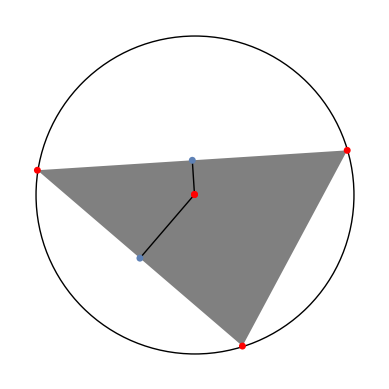

```mathematica
Show[
	Graphics[Circle[center, Norm[pointList[[1]] - center]]],
	Graphics[{Gray,Triangle[pointList]}],
	Graphics[Line[{midPoint[[2]], center}]],
	Graphics[Line[{midPoint[[1]], center}]],
	ListPlot[pointList, PlotStyle->Red],
	ListPlot[midPoint],
	ListPlot[{center}, PlotStyle->Red],
	PlotRange->All
]
```